```mathematica
cmat=Import["~/Downloads/cmatrix.txt","Table"]
vals=Import["~/Downloads/eigenvalues.txt","Table"]
vecs=Import["~/Downloads/eigenvectors.txt","Table"]
```

{{0.5,0.428814,6.19381×10^-10,-0.178831,-5.211×10^-10,0.123443,2.84218×10^-10,-0.101405,-2.98955×10^-10,0.0928281},{0.428814,0.5,0.249983,-5.25233×10^-11,-0.0553877,1.2469×10^-10,0.0220375,4.78716×10^-11,-0.00857738,-6.80465×10^-12},{6.19381×10^-10,0.249983,0.5,0.373426,6.22856×10^-10,-0.156793,-5.86748×10^-10,0.114866,4.26429×10^-10,-0.101405},{-0.178831,-5.25233×10^-11,0.373426,0.5,0.272021,-1.97899×10^-10,-0.0639651,2.9253×10^-10,0.0220375,-4.9388×10^-10},{-5.211×10^-10,-0.0553877,6.22856×10^-10,0.272021,0.5,0.364849,4.24674×10^-10,-0.156793,-2.68693×10^-10,0.123443},{0.123443,1.2469×10^-10,-0.156793,-1.97899×10^-10,0.364849,0.5,0.272021,-5.15847×10^-10,-0.0553877,6.90292×10^-10},{2.84218×10^-10,0.0220375,-5.86748×10^-10,-0.0639651,4.24674×10^-10,0.272021,0.5,0.373426,1.94369×10^-10,-0.178831},{-0.101405,4.78716×10^-11,0.114866,2.9253×10^-10,-0.156793,-5.15847×10^-10,0.373426,0.5,0.249983,-8.04175×10^-10},{-2.98955×10^-10,-0.00857738,4.26429×10^-10,0.0220375,-2.68693×10^-10,-0.0553877,1.94369×10^-10,0.249983,0.5,0.428814},{0.0928281,-6.80465×10^-12,-0.101405,-4.9388×10^-10,0.123443,6.90292×10^-10,-0.178831,-8.04175×10^-10,0.428814,0.5}}

{{-4.6594×10^-7,0,0,0,0,0,0,0,0,0},{0,-3.76763×10^-7,0,0,0,0,0,0,0,0},{0,0,-1.80201×10^-7,0,0,0,0,0,0,0},{0,0,0,1.53586×10^-7,0,0,0,0,0,0},{0,0,0,0,6.82539×10^-7,0,0,0,0,0},{0,0,0,0,0,0.999999,0,0,0,0},{0,0,0,0,0,0,1.,0,0,0},{0,0,0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,0,0,1.}}

{{-0.378571,0.296503,0.429555,0.157074,-0.244092,-0.243969,0.156975,-0.429529,-0.294261,0.380465},{0.307615,-0.265435,-0.380987,0.174559,0.399118,-0.398809,-0.174753,-0.381169,-0.263658,0.309204},{0.134763,-0.0438193,0.109669,-0.541622,-0.417777,-0.417372,-0.541827,-0.110121,0.0431389,-0.135041},{-0.432336,0.341791,-0.132182,0.290411,0.307334,-0.307081,-0.290513,-0.13254,0.339764,-0.433932},{0.233711,-0.474427,0.375182,0.258851,-0.111947,-0.111949,0.258854,-0.374956,0.473712,-0.235515},{0.235502,0.473292,-0.375494,-0.258844,-0.111973,0.111923,0.258861,-0.374644,0.474848,0.233721},{-0.4339,-0.339681,0.13281,-0.290487,0.307126,0.307289,-0.290437,-0.131911,0.341874,0.432367},{0.134998,0.0431223,-0.110032,0.541847,-0.417386,0.417763,-0.541602,-0.109758,0.0438363,0.134806},{0.309245,0.26401,0.380862,-0.174892,0.398777,0.39915,-0.17442,-0.381295,-0.265083,-0.307574},{-0.380491,-0.294718,-0.429271,-0.156819,-0.24393,0.244131,0.15723,-0.429812,-0.296045,-0.378546}}

```mathematica
eigs=Eigensystem[cmat]
```

{{1.,1.,1.,1.,0.999999,6.82539×10^-7,-4.6594×10^-7,-3.76763×10^-7,-1.80201×10^-7,1.53586×10^-7},{{-0.380465,-0.309204,0.135041,0.433932,0.235515,-0.233721,-0.432367,-0.134806,0.307574,0.378546},{-0.294261,-0.263658,0.0431389,0.339764,0.473712,0.474848,0.341874,0.0438363,-0.265083,-0.296045},{0.429529,0.381169,0.110121,0.13254,0.374956,0.374644,0.131911,0.109758,0.381295,0.429812},{0.156975,-0.174753,-0.541827,-0.290513,0.258854,0.258861,-0.290437,-0.541602,-0.17442,0.15723},{0.243969,0.398809,0.417372,0.307081,0.111949,-0.111923,-0.307289,-0.417763,-0.39915,-0.244131},{-0.244092,0.399118,-0.417777,0.307334,-0.111947,-0.111973,0.307126,-0.417386,0.398777,-0.24393},{0.378571,-0.307615,-0.134763,0.432336,-0.233711,-0.235502,0.4339,-0.134998,-0.309245,0.380491},{0.296503,-0.265435,-0.0438193,0.341791,-0.474427,0.473292,-0.339681,0.0431223,0.26401,-0.294718},{0.429555,-0.380987,0.109669,-0.132182,0.375182,-0.375494,0.13281,-0.110032,0.380862,-0.429271},{0.157074,0.174559,-0.541622,0.290411,0.258851,-0.258844,-0.290487,0.541847,-0.174892,-0.156819}}}

```mathematica
cmat//MatrixForm
```

(0.5 | 0.428814 | 6.19381×10^-10 | -0.178831 | -5.211×10^-10 | 0.123443 | 2.84218×10^-10 | -0.101405 | -2.98955×10^-10 | 0.0928281
0.428814 | 0.5 | 0.249983 | -5.25233×10^-11 | -0.0553877 | 1.2469×10^-10 | 0.0220375 | 4.78716×10^-11 | -0.00857738 | -6.80465×10^-12
6.19381×10^-10 | 0.249983 | 0.5 | 0.373426 | 6.22856×10^-10 | -0.156793 | -5.86748×10^-10 | 0.114866 | 4.26429×10^-10 | -0.101405
-0.178831 | -5.25233×10^-11 | 0.373426 | 0.5 | 0.272021 | -1.97899×10^-10 | -0.0639651 | 2.9253×10^-10 | 0.0220375 | -4.9388×10^-10
-5.211×10^-10 | -0.0553877 | 6.22856×10^-10 | 0.272021 | 0.5 | 0.364849 | 4.24674×10^-10 | -0.156793 | -2.68693×10^-10 | 0.123443
0.123443 | 1.2469×10^-10 | -0.156793 | -1.97899×10^-10 | 0.364849 | 0.5 | 0.272021 | -5.15847×10^-10 | -0.0553877 | 6.90292×10^-10
2.84218×10^-10 | 0.0220375 | -5.86748×10^-10 | -0.0639651 | 4.24674×10^-10 | 0.272021 | 0.5 | 0.373426 | 1.94369×10^-10 | -0.178831
-0.101405 | 4.78716×10^-11 | 0.114866 | 2.9253×10^-10 | -0.156793 | -5.15847×10^-10 | 0.373426 | 0.5 | 0.249983 | -8.04175×10^-10
-2.98955×10^-10 | -0.00857738 | 4.26429×10^-10 | 0.0220375 | -2.68693×10^-10 | -0.0553877 | 1.94369×10^-10 | 0.249983 | 0.5 | 0.428814
0.0928281 | -6.80465×10^-12 | -0.101405 | -4.9388×10^-10 | 0.123443 | 6.90292×10^-10 | -0.178831 | -8.04175×10^-10 | 0.428814 | 0.5)

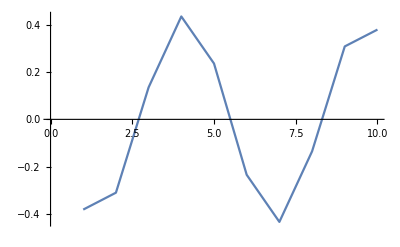
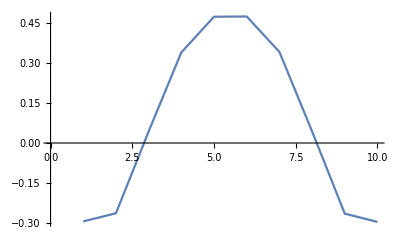
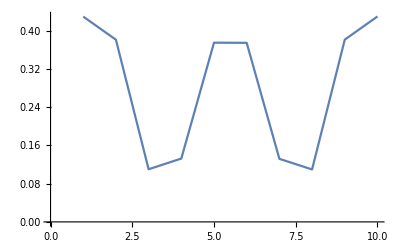
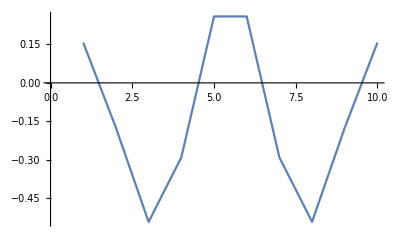
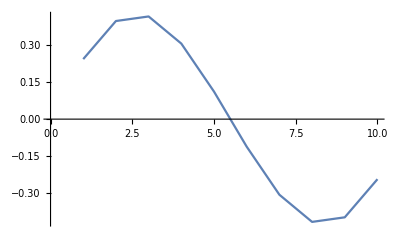
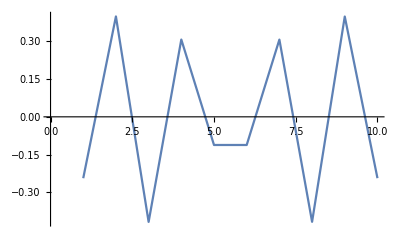
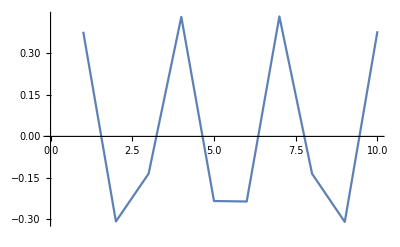
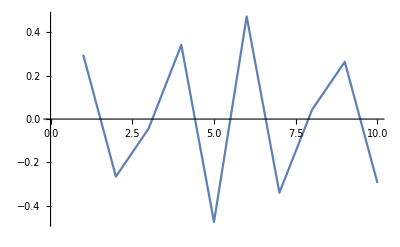

```mathematica
k=10;
Table[ListLinePlot[eigs[[2,k]]],{k,1,10}]
Table[ListLinePlot[vecs[[k]]],{k,1,10}]
```